```mathematica
m=1; m2=0.3;λ=1; g=1; hbar=1; c=0.1; λ2=0; ϵ=0.02;  
kr= √((m/2)^2-m2^2) //N
krs=√((2m)^2-m^2)//N
ωe=m √(1-ϵ^2);
H=0;
Γ=0;
Γd=c^2/(2 m^3)If[m>2 m2,1/√(1-((2 m2)/m)^2),0];1/Γd;
```

0.4

1.73205

```mathematica
(*kw=m;*)
tend=300;

ω[k_]:=√(k^2+m2^2);
χi[k_]:=(ω[k]/π)^(-1/2)
χid[k_]:=I ω[k]χi[k]
```

```mathematica
xo=m^-1 ϵ^-1;
f[k_]:=π xo Sech[k(π xo)/2]

xw=400;
L=2 xw;

ΦH=0.1;
ΦO=ΦH √((m L ϵ)/2);
ϕpH[t_]:= ΦH Sin[m t]
ϕpO[t_]:= ΦO Sin[ωe t]

sm[k_]:=If[k==0,1,1/2 k π xo Csch[k (π xo)/2]]
fp[t_,k_]:=2xo(-λ/2 ϕpO[t]^2+g/(4!)ϕpO[t]^4 1/6(4+k^2 xo^2))sm[k]

EH=L/2 m^2 ΦH^2; NH=EH/m;
EO=m/ϵ ΦO^2;

nmin=30; nmax=70;
Nv=nmax-nmin+1;
kv=N[Table[(2 π n)/L,{n,nmin,nmax}]]
kvmn=kv[[1]];
kvmx=kv[[Nv]];
```

{0.235619,0.243473,0.251327,0.259181,0.267035,0.274889,0.282743,0.290597,0.298451,0.306305,0.314159,0.322013,0.329867,0.337721,0.345575,0.353429,0.361283,0.369137,0.376991,0.384845,0.392699,0.400553,0.408407,0.416261,0.424115,0.431969,0.439823,0.447677,0.455531,0.463385,0.471239,0.479093,0.486947,0.494801,0.502655,0.510509,0.518363,0.526217,0.534071,0.541925,0.549779}

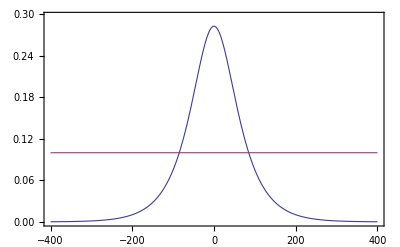

```mathematica
Plot[{ΦO Sech[x/xo],ΦH},{x,-xw,xw},PlotRange->{0,1.05ΦO},Frame->True,PlotStyle->Thickness[0.002],Axes->False]
```

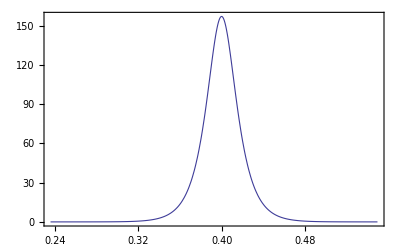

```mathematica
Plot[{f[k-kr]},{k,kvmn,kvmx},PlotRange->All,Frame->True,Axes->False,PlotStyle->Thickness[0.002]]
```

```mathematica
(*Plot[{fp[1,k-krs]},{k,kvmn,kvmx},PlotRange->All,Frame->True,Axes->False,PlotStyle->Thickness[0.002]]*)
```

```mathematica
ϕv=First[ NDSolve[{D[χ[t,k],t,t]+(ω[k]^2+2c ϕpH[t])χ[t,k]==0,χ[0,k]==χi[k],Derivative[1,0][χ][0,k]==χid[k](*,Derivative[0,1][χ][t,-kw]==Derivative[0,1][χ][t,kw]*)},{χ},{t,0,tend},{k,kvmn,kvmx},MaxStepFraction->1/800,PrecisionGoal->4]];
```

```mathematica
eqns=Table[{Subscript[χ, j]''[t]+ω[kv[[j]]]^2 Subscript[χ, j][t]+2c ϕpO[t]Sum[1/L f[kv[[j]]-kv[[jp]]]Subscript[χ, jp][t],{jp,1,Nv}]==0,Subscript[χ, j][0]==χi[kv[[j]]],Subscript[χ, j]'[0]==χid[kv[[j]]]},{j,1,Nv}];
vars=Table[Subscript[χ, j],{j,1,Nv}];
ϕvS=First[NDSolve[eqns,vars,{t,0,tend}]];
```

```mathematica
(*eqns2=Table[{Subscript[χ, j]''[t]+(kv[[j]]^2+m^2)Subscript[χ, j][t]+Sum[1/L fp[t,kv[[j]]-kv[[jp]]]Subscript[χ, jp][t],{jp,1,Nv}]==0,Subscript[χ, j][0]==χi[kv[[j]]],Subscript[χ, j]'[0]==χid[kv[[j]]]},{j,1,Nv}];
vars2=Table[Subscript[χ, j],{j,1,Nv}];
ϕvS2=First[NDSolve[eqns2,vars2,{t,0,tend}]];*)
```

```mathematica
eqnsF=Table[{Subscript[χ, q,j]''[t]+ω[kv[[j]]]^2 Subscript[χ, q,j][t]+2c ϕpO[t]Sum[1/L f[kv[[j]]-kv[[jp]]]Subscript[χ, q,jp][t],{jp,1,Nv}]==0,Subscript[χ, q,j][0]==If[q==j,L/(2 π)χi[kv[[j]]],0],Subscript[χ, q,j]'[0]==If[q==j,L/(2 π)χid[kv[[j]]],0]},{j,1,Nv},{q,1,Nv}];
varsF=Table[Subscript[χ, q,j],{j,1,Nv},{q,1,Nv}];
ϕvSF=Table[First[NDSolve[eqnsF[[All,q]],varsF[[All,q]],{t,0,tend}]],{q,1,Nv}];
```

```mathematica
(*eqnsF2=Table[{Subscript[χ, q,j]''[t]+(kv[[j]]^2+m^2)Subscript[χ, q,j][t]+Sum[1/L fp[t,kv[[j]]-kv[[jp]]]Subscript[χ, q,jp][t],{jp,1,Nv}]==0,Subscript[χ, q,j][0]==If[q==j,L/(2 π)χi[kv[[j]]],0],Subscript[χ, q,j]'[0]==If[q==j,L/(2 π)χid[kv[[j]]],0]},{j,1,Nv},{q,1,Nv}];
varsF2=Table[Subscript[χ, q,j],{j,1,Nv},{q,1,Nv}];
ϕvSF2=Table[First[NDSolve[eqnsF2[[All,q]],varsF2[[All,q]],{t,0,tend}]],{q,1,Nv}];*)
```

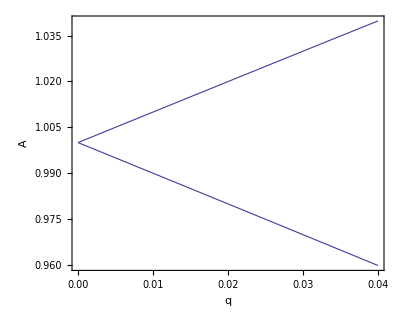

0.41225

0.387234

```mathematica
qv=(4 c ΦH)/m^2;
Av[k_]:=4 ω[k]^2/m^2;
Plot[{Table[{MathieuCharacteristicA[r,q],MathieuCharacteristicB[r,q]},{r,1,1}]},{q,0,qv},Frame->True,AspectRatio->0.8,PlotStyle->Thickness[0.002],FrameLabel->{"q","A"},FrameStyle->18,Axes->False]
kA=-k/.First[First[Solve[Av[k]==MathieuCharacteristicA[1,qv],k]]]
kB=-k/.First[First[Solve[Av[k]==MathieuCharacteristicB[1,qv],k]]]
```

```mathematica
Animate[ListPlot[{(*Table[{kv[[j]],1/(2 π)(1/2 Abs[Derivative[1][Subscript[χ, j]][t]]^2+1/2(kv[[j]]^2+m2^2)Abs[Subscript[χ, j][t]]^2)/.ϕvS},{j,1,Nv}],*)Table[{kv[[j]],1/(2 π)Sum[((2π)/L)^2(1/2 Abs[Derivative[1][Subscript[χ, q,j]][t]]^2+1/2(kv[[j]]^2+m2^2)Abs[Subscript[χ, q,j][t]]^2)/.ϕvSF[[q]],{q,1,Nv}]},{j,1,Nv}],Table[{kv[[j]],1/(2 π)(1/2 Abs[Derivative[1,0][χ][t,kv[[j]]]]^2+1/2(kv[[j]]^2+m2^2)Abs[χ[t,kv[[j]]]]^2)/.ϕv},{j,1,Nv}],Table[{kv[[j]],1/2 √(kv[[j]]^2+m2^2)},{j,1,Nv}](*,Table[{kv[[j]],10^8(kv[[j]]-kA)},{j,1,Nv}],Table[{kv[[j]],10^8(kv[[j]]-kB)},{j,1,Nv}]*)},PlotRange->{{kvmn,kvmx},{0,4}},PlotStyle->Thickness[0.0015],AspectRatio->0.3,ImageSize->1000,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Wavenumber k","Energy density E_k",t},FrameStyle->18],{t,0,tend},AnimationRate->5]
```

```mathematica
(*Animate[Plot[{Abs[χ[t,k]]^2/.ϕv,χ[0,0] E^(Γd t/2)/.ϕv},{k,0,kw},PlotRange->{0,20},PlotStyle->Thickness[0.001],AspectRatio->0.3,ImageSize->1000],{t,0,tend}]*)
```

```mathematica
Mpr[t_,k_]:=If[kA> k>kB,EH Γd t,0]
```

```mathematica
χex[t_,k_]:=(√π √(1/ω[k]) ((-2 ⅈ ω[k] MathieuC[Av[k],qv,0]+m MathieuCPrime[Av[k],qv,0]) MathieuS[Av[k],qv,m/2 t]+MathieuC[Av[k],qv,m/2 t] (2 ⅈ ω[k] MathieuS[Av[k],qv,0]-m MathieuSPrime[Av[k],qv,0])))/(m (MathieuCPrime[Av[k],qv,0] MathieuS[Av[k],qv,0]-MathieuC[Av[k],qv,0] MathieuSPrime[Av[k],qv,0]))
```

```mathematica
Animate[Plot[{Re[χ[t,k]]/.ϕv,Re[χex[t,k]](*,10^8(k-kA),10^8(k-kB)*)},{k,kvmn,kvmx},PlotRange->{{kvmn,kvmx},{-20,20}},PlotStyle->Thickness[0.0015],AspectRatio->0.3,ImageSize->1000,Frame->True,FrameLabel->{"Wavenumber k","Energy density E_k",t},FrameStyle->18],{t,0,tend},AnimationRate->6]
```

```mathematica
Animate[Plot[{1/(2 π)(1/2 Abs[Derivative[1,0][χ][t,k]]^2+1/2(k^2+m2^2)Abs[χ[t,k]]^2)-1/2 √(k^2+m2^2)/.ϕv,
1/(2 π)(1/2 Abs[Derivative[1,0][χex][t,k]]^2+1/2(k^2+m2^2)Abs[χex[t,k]]^2)-1/2 √(k^2+m2^2)(*,10^8(k-kA),10^8(k-kB)*)},{k,kvmn,kvmx},PlotRange->{{kvmn,kvmx},{-0.1,5}},PlotStyle->Thickness[0.0015],AspectRatio->0.3,ImageSize->1000,Frame->True,FrameLabel->{"Wavenumber k","Energy density E_k",t},FrameStyle->18],{t,0,tend},AnimationRate->6]
```

```mathematica
tvmin=10; tvmax=300; tvstep=10;
```

```mathematica
dtab=Table[{tv,NIntegrate[L/(2 π)(1/(2 π)(1/2 Abs[Derivative[1,0][χ][tv,k]]^2+1/2(k^2+m2^2)Abs[χ[tv,k]]^2)-1/2 √(k^2+m2^2))/.ϕv,{k,0.3,0.5},AccuracyGoal->3]},{tv,tvmin,tvmax,tvstep}];
```

```mathematica
dtabex=Table[{tv,NIntegrate[L/(2 π)(1/(2 π)(1/2 Abs[Derivative[1,0][χex][tv,k]]^2+1/2(k^2+m2^2)Abs[χex[tv,k]]^2)-1/2 √(k^2+m2^2)),{k,0.3,0.5},AccuracyGoal->3]},{tv,tvmin,tvmax,tvstep}];
```

```mathematica
dtabp=Table[{tv,EH Γd tv},{tv,tvmin,tvmax,tvstep}];
```

```mathematica
dtabp2=Table[{tv,EH(E^(Γd tv)-1)},{tv,tvmin,tvmax,tvstep}];
```

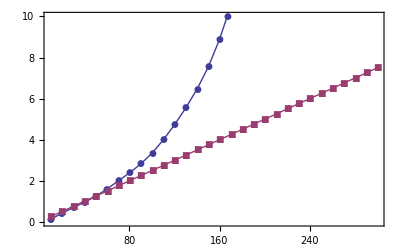

```mathematica
ListPlot[{dtabex,dtabp},Joined->True,ImageSize->400,Frame->True,FrameStyle->15,Axes->False,PlotMarkers->Automatic,PlotRange->{0,10}]
```

```mathematica
Simplify[DSolve[{y''[z]+(Ak-2 qk Cos[2 z])y[z]==0,y[0]==√(π/ωk),y'[0]==2/mo I ωk √(π/ωk)},y[z],z]]
```

{{y[z]→(√π √(1/ωk) ((-2 ⅈ ωk MathieuC[Ak,qk,0]+mo MathieuCPrime[Ak,qk,0]) MathieuS[Ak,qk,z]+MathieuC[Ak,qk,z] (2 ⅈ ωk MathieuS[Ak,qk,0]-mo MathieuSPrime[Ak,qk,0])))/(mo (MathieuCPrime[Ak,qk,0] MathieuS[Ak,qk,0]-MathieuC[Ak,qk,0] MathieuSPrime[Ak,qk,0]))}}